## Definiciones

```mathematica
Get["~/Documents/libs/QMB.wl"]
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
?Superoperator
```

## Ising

## 10^6 s<=t<=10^6+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^4,10^4+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.274064,0.294218,0.279685,0.265049,0.27145,0.270894,0.264873,0.264505,0.274722,0.274878,0.265842,0.27659,0.282131,0.276571,0.27428,0.280889,0.287604,0.277002,0.276766,0.276526,0.283915,0.270996,0.272008,0.275219,0.280184,0.273481,0.278731,0.272476,0.261896,0.274107,0.294752,0.28188,0.272267,0.275271,0.274657,0.268606,0.261119,0.27167,0.279388,0.265713,0.258276,0.270277,0.276749,0.282985,0.286886,0.277272,0.269227,0.270864,0.276499,0.273879,0.271388}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.426462,0.426867,0.428737,0.42956,0.431286,0.432879,0.434124,0.436371,0.437308,0.439528,0.440675,0.442137,0.44384,0.444356,0.446325,0.446347,0.447771,0.44797,0.448221,0.448911,0.448092,0.448945,0.447746,0.448079,0.447174,0.446611,0.446178,0.444998,0.444727,0.443545,0.443058,0.442231,0.441516,0.440905,0.440327,0.439596,0.439464,0.438546,0.438703,0.437956,0.43789,0.437774,0.437138,0.43772,0.436711,0.437473,0.4367,0.436931,0.436908,0.43634,0.43704}

### Gráfica

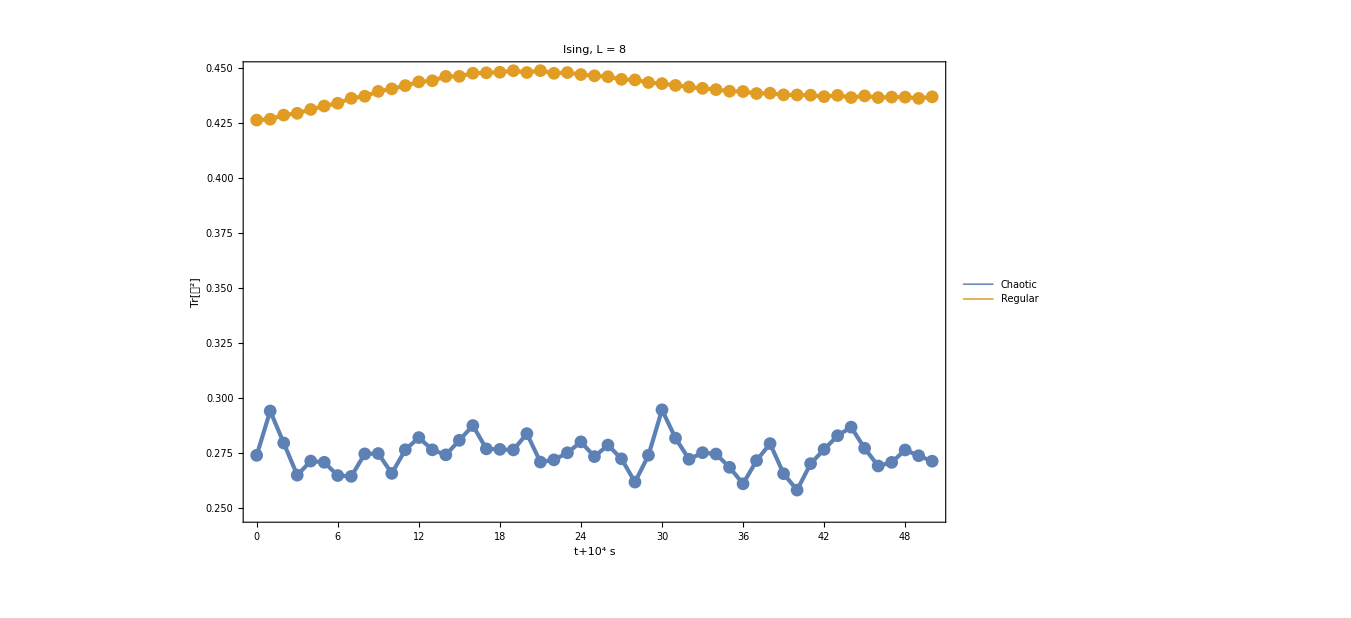

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^4s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^6 s<=t<=10^6+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^5,10^5+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.271912,0.266041,0.262856,0.261555,0.261508,0.268535,0.262842,0.264504,0.26212,0.263071,0.269431,0.27166,0.266616,0.266588,0.268648,0.264777,0.268215,0.261882,0.263497,0.269365,0.267445,0.260253,0.257778,0.257992,0.258961,0.26481,0.269461,0.270619,0.273241,0.26865,0.264856,0.262516,0.259074,0.25731,0.262816,0.263909,0.264929,0.264222,0.264293,0.260052,0.264447,0.262262,0.265594,0.266274,0.26332,0.266602,0.273291,0.280594,0.275566,0.266551,0.279391}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.345908,0.345985,0.346082,0.346012,0.346151,0.346005,0.346094,0.345959,0.345972,0.345829,0.345751,0.345561,0.345395,0.345216,0.344965,0.344881,0.344552,0.34456,0.344222,0.344237,0.344025,0.343964,0.343971,0.343861,0.344053,0.344009,0.344228,0.344329,0.344455,0.344699,0.344803,0.345099,0.345323,0.345511,0.34588,0.345906,0.346348,0.346364,0.346746,0.346934,0.347135,0.347548,0.347607,0.348158,0.348267,0.34879,0.349112,0.349516,0.35006,0.350429,0.351042}

### Gráfica

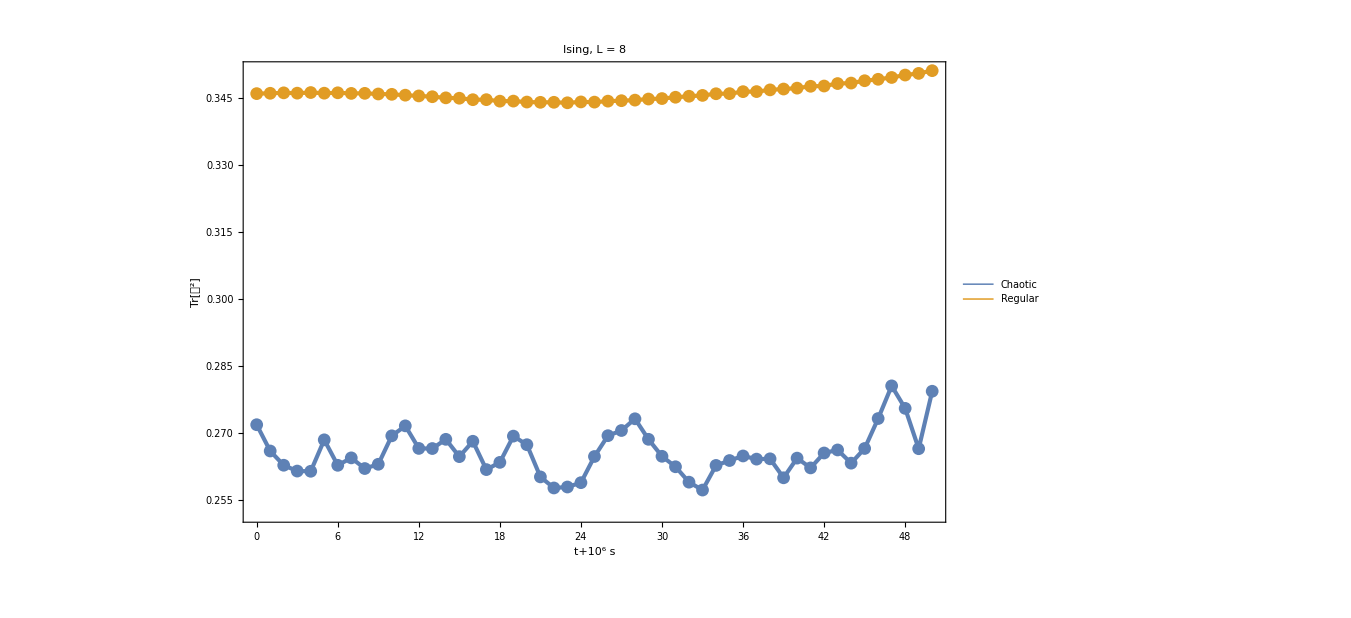

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^6s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^6 s<=t<=10^6+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^6,10^6+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.255359,0.256668,0.254312,0.255263,0.255364,0.264502,0.263225,0.257536,0.257464,0.259345,0.258925,0.260403,0.261167,0.256479,0.2585,0.257029,0.255825,0.25674,0.261966,0.266554,0.258182,0.259054,0.259925,0.256089,0.260307,0.262923,0.265689,0.264862,0.263489,0.264362,0.265825,0.265486,0.257794,0.263869,0.268424,0.257453,0.255884,0.254452,0.25559,0.25663,0.257344,0.260294,0.264685,0.259334,0.256441,0.257562,0.260108,0.258263,0.262273,0.261074,0.256522}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.3035,0.303236,0.304231,0.303888,0.304652,0.304694,0.304961,0.305616,0.305399,0.30641,0.306004,0.306863,0.306739,0.307074,0.307529,0.307281,0.308153,0.307595,0.308422,0.308025,0.308402,0.308485,0.308266,0.308742,0.308102,0.308608,0.307956,0.308165,0.307834,0.307621,0.307614,0.307076,0.307129,0.306527,0.306399,0.306007,0.305668,0.305567,0.305153,0.305164,0.304847,0.304718,0.304654,0.304347,0.304615,0.304321,0.304775,0.304704,0.305031,0.305298,0.305332}

### Gráfica

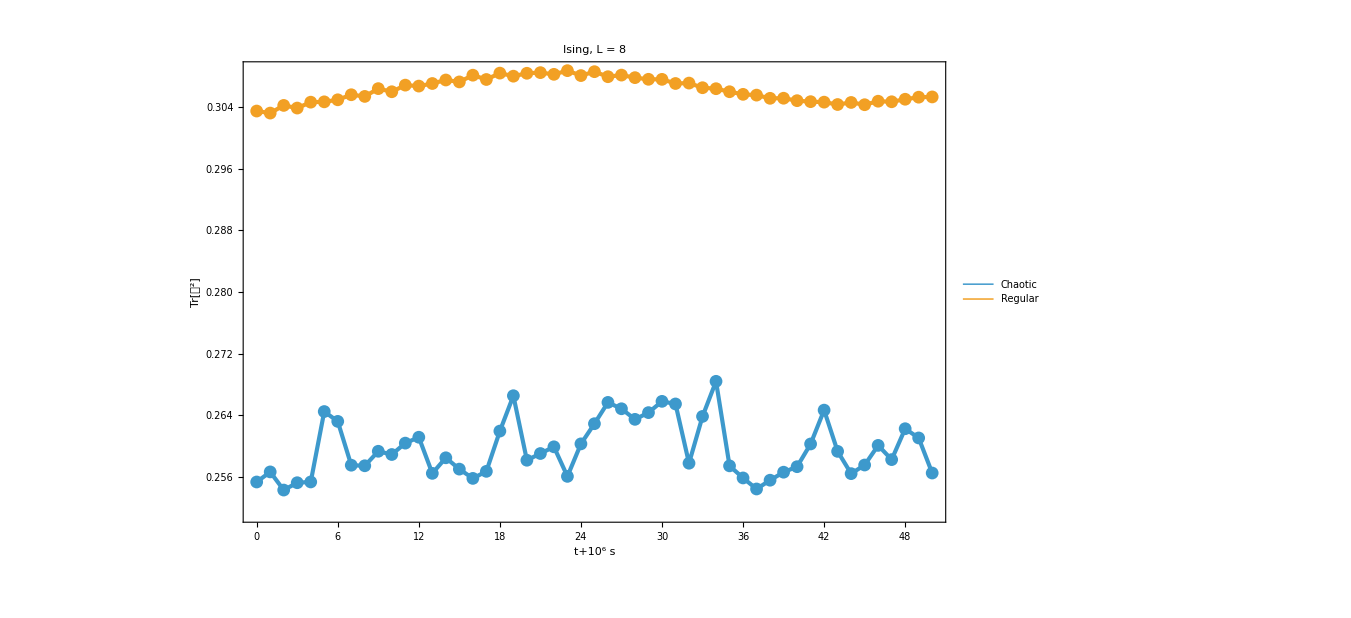

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^6s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^9 s<=t<=10^9+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^9,10^9+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.254601,0.259845,0.256731,0.261121,0.257835,0.259817,0.261369,0.257158,0.257313,0.257778,0.266597,0.270853,0.259092,0.265966,0.263257,0.261102,0.266629,0.257649,0.256759,0.262489,0.260154,0.257053,0.263486,0.256906,0.257525,0.265608,0.266328,0.265544,0.258081,0.256561,0.256711,0.256759,0.26041,0.256474,0.258971,0.255049,0.259832,0.255067,0.260091,0.262524,0.260351,0.261133,0.257039,0.258638,0.26111,0.25859,0.253109,0.25992,0.261264,0.257902,0.266156}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.320424,0.320543,0.32111,0.321271,0.321761,0.321996,0.322319,0.322639,0.322699,0.323093,0.322878,0.32328,0.322902,0.323168,0.322799,0.322755,0.322519,0.322094,0.322008,0.321291,0.321269,0.320447,0.320364,0.319621,0.319397,0.31885,0.318464,0.318148,0.31761,0.317487,0.31683,0.316821,0.316142,0.316144,0.315591,0.315488,0.315168,0.314868,0.314777,0.314285,0.31433,0.31378,0.313839,0.313403,0.313376,0.313137,0.312975,0.312921,0.312659,0.312749,0.312499}

### Gráfica

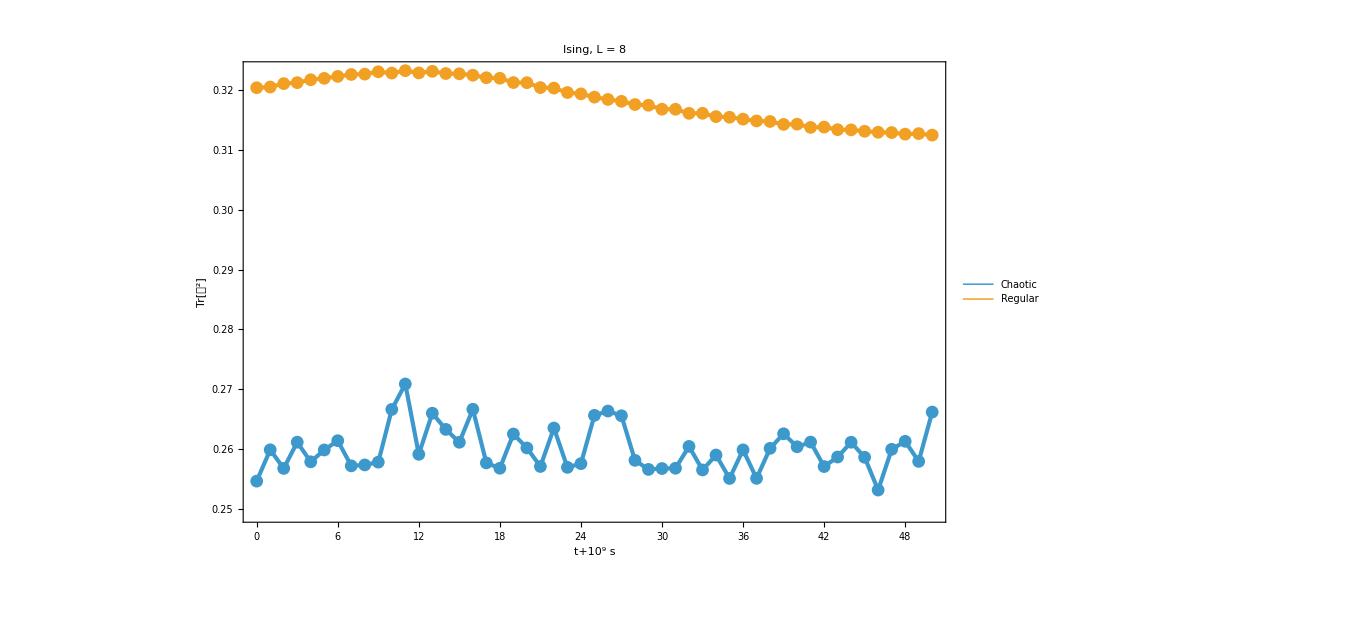

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^9s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^12 s<=t<=10^12+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^12,10^12+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.265808,0.258846,0.257834,0.255803,0.257725,0.254987,0.252317,0.252514,0.255864,0.256589,0.260635,0.259716,0.25486,0.255932,0.261004,0.256323,0.259885,0.263348,0.262074,0.260126,0.256597,0.259406,0.261892,0.264786,0.259606,0.25377,0.257833,0.257515,0.256469,0.255567,0.256609,0.257495,0.261874,0.259382,0.257661,0.253251,0.263585,0.258943,0.253636,0.256913,0.255124,0.256332,0.26088,0.259088,0.255234,0.255683,0.256083,0.258289,0.256417,0.256775,0.253359}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.293789,0.294508,0.294681,0.295498,0.295837,0.29647,0.296957,0.29733,0.297998,0.298268,0.29904,0.299324,0.299926,0.300228,0.300519,0.300808,0.300929,0.301192,0.301317,0.301421,0.301526,0.301406,0.301404,0.301185,0.301061,0.300969,0.30068,0.300679,0.300205,0.300151,0.299613,0.299459,0.29906,0.298818,0.298606,0.298197,0.29805,0.297448,0.297344,0.296715,0.296688,0.29618,0.296127,0.29573,0.295436,0.295182,0.294647,0.294644,0.294015,0.294226,0.293601}

### Gráfica

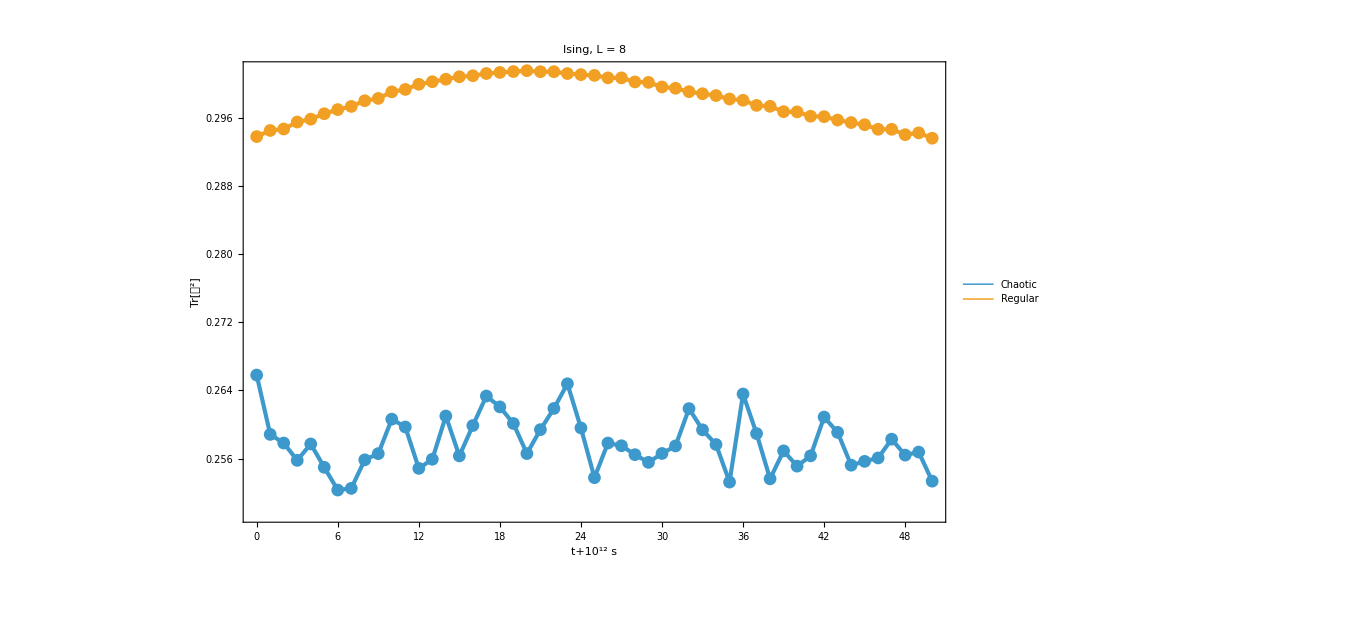

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^12s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^15 s<=t<=10^15+60s

```mathematica
L=8;
hx=1.;
```

```mathematica
t=Range[10^15,10^15+50,1.];
```

### Caótico

```mathematica
{hz,J} = {0.48,0.8};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.264641,0.267411,0.266009,0.269797,0.26313,0.254596,0.260841,0.260308,0.260962,0.260767,0.256711,0.254279,0.255157,0.252819,0.254929,0.257605,0.256183,0.263655,0.262108,0.258168,0.257263,0.268222,0.265086,0.268755,0.26257,0.258562,0.261349,0.265976,0.260593,0.257644,0.257718,0.255725,0.253676,0.25917,0.260829,0.262222,0.263198,0.256331,0.257521,0.256132,0.259067,0.258716,0.265435,0.269548,0.257783,0.2589,0.258305,0.258653,0.265702,0.26335,0.259255}

### Regular

```mathematica
{hz,J} = {1.446,0.05};

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;
```

```mathematica
purityRegular=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.30877,0.308373,0.307595,0.310555,0.309817,0.307975,0.307541,0.307,0.308017,0.309686,0.308323,0.307172,0.310947,0.307502,0.307404,0.307141,0.306904,0.309926,0.310765,0.31141,0.309497,0.310265,0.310301,0.310315,0.307844,0.306661,0.307716,0.30698,0.309224,0.308757,0.306889,0.306914,0.308094,0.303207,0.305496,0.306692,0.308043,0.304049,0.307328,0.306404,0.304958,0.305704,0.306742,0.306812,0.305169,0.308133,0.310502,0.308964,0.311035,0.309804,0.30904}

### Gráfica

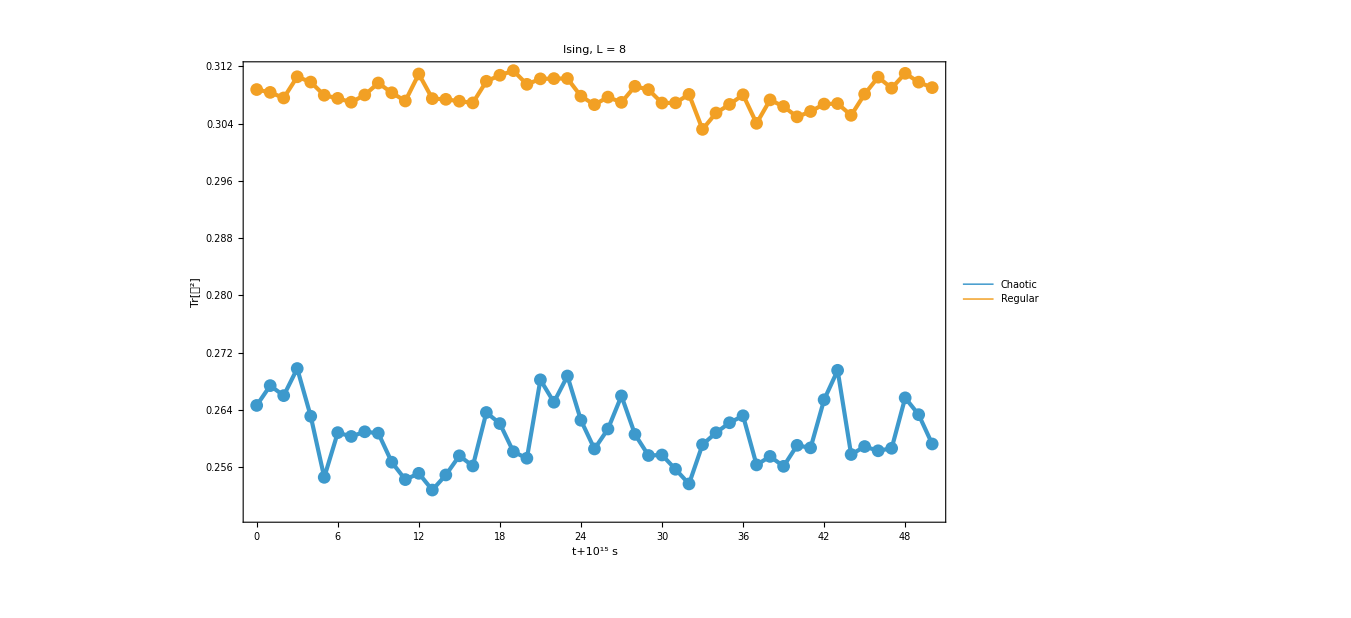

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^15s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## XXZ

## 0s<=t<=50s

```mathematica
L = 7;(* espines *)
d = 3;(* defecto *)
Jz = 1;
ω = 0;
```

```mathematica
t=Range[0,50,0.5];
```

### Caótico

```mathematica
{ε,Jxy}={2.,2.};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{1.,0.814445,0.507348,0.407937,0.408552,0.392374,0.418603,0.403429,0.333931,0.32544,0.32006,0.29086,0.288753,0.311079,0.304292,0.285662,0.283244,0.284804,0.280448,0.280518,0.281445,0.280734,0.291297,0.297576,0.291703,0.282886,0.279322,0.280398,0.272716,0.272697,0.274768,0.274621,0.282331,0.302738,0.3037,0.284808,0.270674,0.265054,0.273123,0.28862,0.305038,0.31376,0.302759,0.287219,0.28138,0.297145,0.302887,0.29366,0.290718,0.295579,0.296699,0.292613,0.285254,0.284875,0.289475,0.291646,0.291407,0.294281,0.293759,0.288922,0.290491,0.292263,0.294467,0.297806,0.301211,0.305608,0.302892,0.290629,0.282957,0.282302,0.288409,0.297944,0.305487,0.297635,0.284999,0.293416,0.304859,0.306394,0.306106,0.294305,0.278046,0.272795,0.276854,0.287945,0.299616,0.29955,0.285057,0.281083,0.293145,0.302533,0.301829,0.295415,0.286353,0.289279,0.296594,0.294075,0.2912,0.28717,0.288119,0.290548,0.29143}

### Regular

```mathematica
{ε,Jxy}={0.05,4.55};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityRegular1=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{1.,0.530386,0.275223,0.289288,0.318123,0.256669,0.301952,0.420863,0.394572,0.275305,0.270536,0.277775,0.284889,0.280921,0.304471,0.284786,0.265925,0.285043,0.299866,0.294391,0.277269,0.279681,0.283626,0.28037,0.278665,0.307574,0.297389,0.295012,0.297219,0.286093,0.272236,0.278096,0.269696,0.2822,0.296869,0.279927,0.264802,0.302353,0.292505,0.279895,0.285714,0.273337,0.259769,0.274828,0.283761,0.313374,0.328793,0.3044,0.293303,0.264905,0.28123,0.304727,0.311598,0.331741,0.318233,0.296046,0.273493,0.267694,0.309009,0.282501,0.284883,0.294162,0.290378,0.271295,0.265232,0.28066,0.279222,0.272752,0.294217,0.295003,0.28408,0.286214,0.280902,0.283271,0.280732,0.276182,0.300946,0.273773,0.269302,0.278335,0.276186,0.274226,0.276802,0.305442,0.288278,0.262144,0.270376,0.279281,0.277673,0.305685,0.290782,0.310777,0.292628,0.284303,0.269223,0.282122,0.272676,0.292227,0.304328,0.321708,0.321954}

```mathematica
{ε,Jxy}={4.5,0.5};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityRegular2=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{1.,0.977444,0.913735,0.829339,0.737972,0.657306,0.598651,0.557378,0.535823,0.525124,0.525274,0.533085,0.547413,0.567405,0.590216,0.611086,0.625206,0.632333,0.630253,0.620195,0.604058,0.582475,0.554808,0.521458,0.485801,0.451585,0.42394,0.406415,0.400074,0.404946,0.418929,0.439979,0.465791,0.4929,0.515619,0.529823,0.532419,0.522264,0.50301,0.479224,0.456242,0.438792,0.42949,0.428673,0.438707,0.460642,0.496678,0.551993,0.622791,0.702427,0.779534,0.837336,0.865485,0.860229,0.826961,0.775736,0.722463,0.674118,0.637496,0.616634,0.603806,0.60088,0.602851,0.60667,0.612709,0.621915,0.632537,0.6482,0.670774,0.696998,0.729791,0.760235,0.78241,0.788706,0.769673,0.72951,0.670921,0.605376,0.542418,0.490865,0.454376,0.430841,0.422369,0.424788,0.436891,0.455565,0.4769,0.495725,0.507262,0.508205,0.498421,0.479463,0.455732,0.432362,0.413141,0.400594,0.395275,0.397963,0.410464,0.432772,0.465824}

### Gráfica

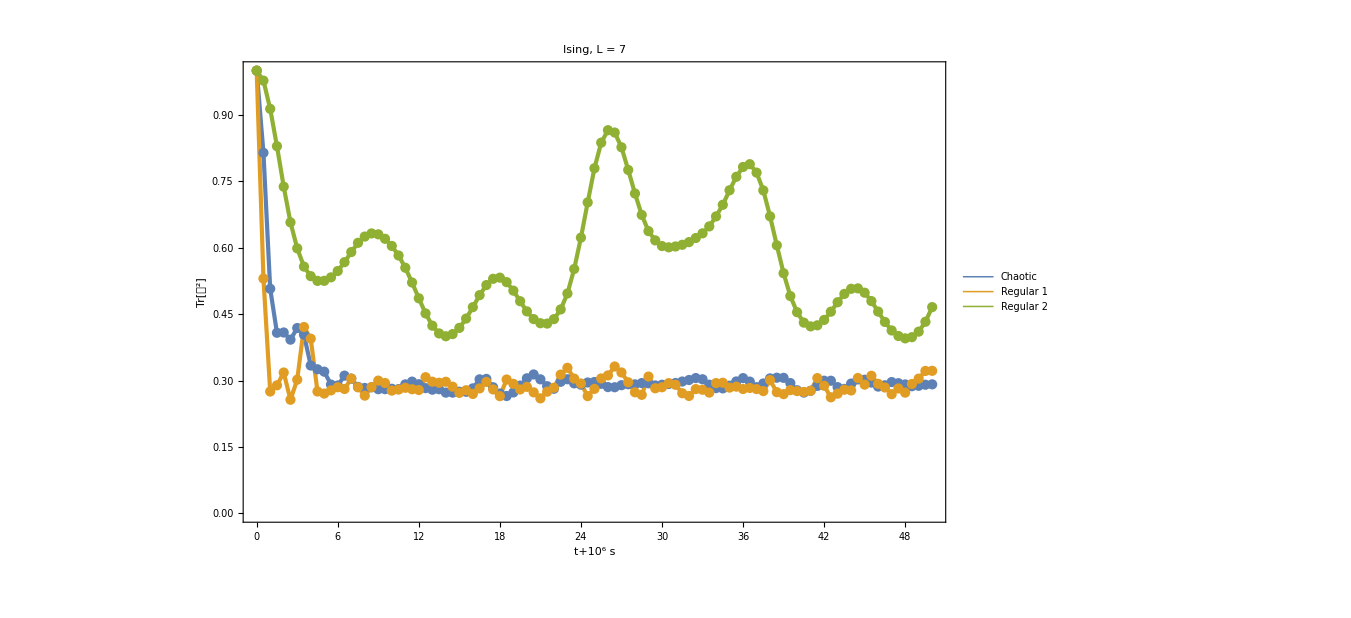

```mathematica
ListPlot[Transpose[{Range[0,50,0.5],#}]&/@{purityChaotic,purityRegular1,purityRegular2},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^6s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular 1","Regular 2"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```

## 10^6 s<=t<=10^6+60s

```mathematica
L = 7;(* espines *)
d = 3;(* defecto *)
Jz = 1;
ω = 0;
```

```mathematica
t=Range[10^6,10^6+50,1.];
```

### Caótico

```mathematica
{ε,Jxy}={2.,2.};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityChaotic=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.29216,0.29363,0.290123,0.281036,0.301781,0.295062,0.304389,0.321961,0.301193,0.285435,0.29034,0.277339,0.284537,0.296789,0.299935,0.267392,0.280654,0.286018,0.269789,0.276177,0.278721,0.310296,0.283018,0.289586,0.300504,0.294596,0.286734,0.279315,0.295272,0.309082,0.280985,0.279634,0.288178,0.269271,0.274802,0.287273,0.292257,0.272158,0.284137,0.28026,0.27969,0.285939,0.272676,0.28158,0.292852,0.276852,0.289413,0.292046,0.279092,0.282947,0.277234}

### Regular

```mathematica
{ε,Jxy}={0.05,4.55};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityRegular1=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.293078,0.270355,0.284235,0.276595,0.274548,0.283026,0.283528,0.294662,0.286979,0.283438,0.283868,0.284137,0.290787,0.290031,0.277412,0.279805,0.289883,0.288231,0.289342,0.280962,0.277356,0.290894,0.293167,0.289079,0.282072,0.257861,0.275924,0.288179,0.26822,0.275665,0.283816,0.282938,0.270839,0.271671,0.293991,0.261062,0.297694,0.295576,0.298643,0.266879,0.287791,0.294576,0.286594,0.284248,0.282672,0.293424,0.280989,0.265522,0.301738,0.274176,0.279525}

```mathematica
{ε,Jxy}={4.5,0.5};

(* Crear Hamiltoniano y diagonalizar *)
H = XXZOpenHamiltonian[Jxy, Jz, ω, ε, L, d];
{eigenvals, eigenvecs} = Chop[Eigensystem[H]];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
```

```mathematica
purityRegular2=Chop[Purity[Reshuffle[Superoperator[#,ψ,eigenvals,eigenvecs,L]]/2.]]&/@t
```

{0.397859,0.396992,0.392695,0.388139,0.385646,0.385283,0.386262,0.388789,0.392036,0.395046,0.395197,0.392643,0.388001,0.384314,0.383013,0.384436,0.389311,0.395165,0.40033,0.400704,0.397955,0.391217,0.384025,0.38042,0.383412,0.390987,0.396797,0.398003,0.395948,0.392458,0.388102,0.384997,0.38309,0.384445,0.388463,0.394159,0.397426,0.396742,0.391056,0.383948,0.379067,0.377277,0.381764,0.389931,0.397782,0.401919,0.400287,0.393489,0.383857,0.377002,0.376893}

### Gráfica

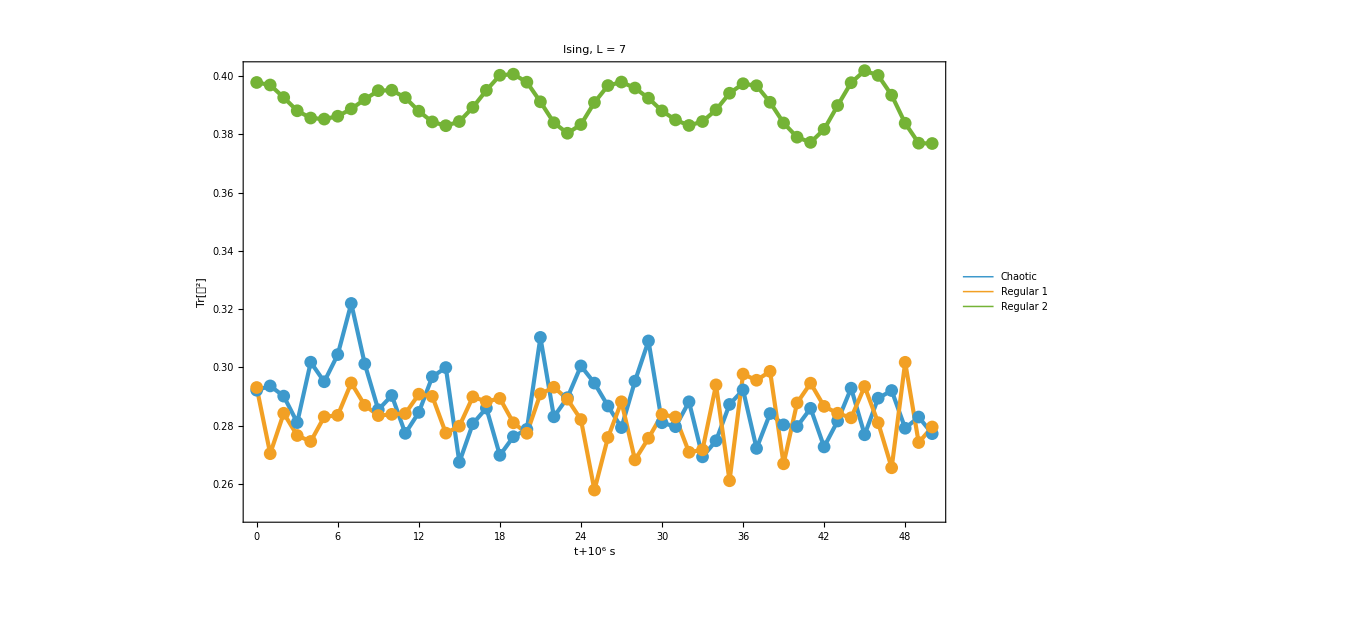

```mathematica
ListPlot[Transpose[{Range[0,50],#}]&/@{purityChaotic,purityRegular1,purityRegular2},
PlotRange->All,
Joined->True,
PlotStyle->Directive[Thickness[0.003]],
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t+10^6s]], TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->30],
PlotLegends->{"Chaotic","Regular 1","Regular 2"},
LabelStyle->Directive[Black,FontSize->25],
ImageSize->1000,
PlotLabel->Style["Ising, L = "<>ToString[L],Black,FontSize->30]
]
```